```mathematica
data=Import["DropBox/HackCDMX15/Datoslimpioschoques/datos2014.csv","CSV",CharacterEncoding->"UTF8"]
```

{{TL - Transito lento,sobre Dr Río de la Loza y su continuación Fray Servando Teresa de Mier desde Balderas hasta Eje 2 Oriente Av. H. Congreso de la Unión.,Circular por Eje 2 Sur (Dr. Balmis y su continuación Av. del Taller),70,(19.4221682,-99.12084099999998),19/05/2014 15:04},33625,{1}}
 |  |  |  |

```mathematica
viadata=Import["Documents/MORLAN/INEGI/shps/df/df_eje_vial.shp","Data"];
vias=viadata[[1,2,2]];
```

```mathematica
munida=Import["Documents/MORLAN/INEGI/shps/df/df_municipal.shp","Data"];
muns=munida[[1,2,2]];
```

```mathematica
metdat=Import["Documents/MORLAN/Transporte DF/lineasmetro2.xls","XLS"];
metro=metdat[[1,2;;-1]];
```

```mathematica
manida=Import["Documents/MORLAN/INEGI/shps/df/df_manzanas.shp","Data"];
mans=manida[[1,2,2]];
```

```mathematica
ecobici=Import["Documents/MORLAN/HackCDMX15/UbiEstEcobici.csv","CSV"];
```

```mathematica
ecobi=ecobici[[2;;-1]];
```

```mathematica
logom=Import["Dropbox/HackCDMX15/logos/metro-logo.png","PNG"];
logoe=Import["Dropbox/HackCDMX15/logos/logoecobici.png","PNG"];
```

```mathematica
acdata=Map[StringTake[#,3]&,data[[All,1]]];
```

```mathematica
pos=Flatten[Position[acdata,_?(#=="ACV"&)]];
```

```mathematica
ndata=data[[pos,{5,6}]];
```

```mathematica
tdata=Map[Flatten[{ToExpression[Reverse[StringSplit[#[[1]],{"(",")",","}]]],StringSplit[#[[2]],{" ",":"}]}]&,ndata];
```

```mathematica
punb=Select[tdata,Length[#]==5&]
```

{{-99.2046,19.4013,24/04/2014,09,20},{-99.0916,19.4766,24/04/2014,00,59},8167,{-99.2113,19.3309,4/8/2014,21,59},{-99.1777,19.3975,4/8/2014,18,28}}
 |  |  |  |

```mathematica
puntos=Point/@punb[[All,{1,2}]];
```

```mathematica
metpo=metro[[All,{5,4}]];
```

```mathematica
Transpose[{Range[Length[metro[[All,3]]]],metro[[All,3]]}]
```

{{1,Observatorio},{2,Tacubaya},{3,Juanacatlan},{4,Chapultepec},{5,Sevilla},{6,Insurgentes},{7,Cuauhtemoc},{8,Balderas},{9,Salto del Agua},{10,Isabel la Catolica},{11,Pino Suarez},{12,Merced},{13,Candelaria},{14,San Lazaro},{15,Moctezuma},{16,Balbuena},{17,Blvd Puerto Aereo},{18,Gomez Farias},{19,Zaragoza},{20,Pantitlan},{21,Cuatro Caminos},{22,Panteones},{23,Tacuba},{24,Cuitlahuac},{25,Popotla},{26,Colegio Militar},{27,Normal},{28,San Cosme},{29,Revolucion},{30,Hidalgo},{31,Bellas Artes},{32,Allende},{33,Zocalo},{34,Pino Suarez},{35,San Antonio Abad},{36,Chabacano},{37,Viaducto},{38,Xola},{39,Villa de Cortes},{40,Nativitas},{41,Portales},{42,Ermita},{43,General Anaya},{44,Tasquena},{45,Indios Verdes},{46,Deportivo 18 de Marzo},{47,Potrero},{48,La Raza},{49,Tlatelolco},{50,Guerrero},{51,Hidalgo},{52,Juarez},{53,Balderas},{54,Ninos Heroes},{55,Hospital General},{56,Centro Medico},{57,Etiopia},{58,Eugenia},{59,Division del Norte},{60,Zapata},{61,Coyoacan},{62,Viveros},{63,Miguel A de Quevedo},{64,Copilco},{65,Universidad},{66,Martin Carrera},{67,Talisman},{68,Bondojito},{69,Consulado},{70,Canal del Norte},{71,Morelos},{72,Candelaria},{73,Fray Servando},{74,Jamaica},{75,Santa Anita},{76,Politecnico},{77,Inst del Petroleo},{78,Autobuses del Norte},{79,La Raza},{80,Misterios},{81,Valle Gomez},{82,Consulado},{83,Eduardo Molina},{84,Aragon},{85,Oceania},{86,Terminal Aerea},{87,Hangares},{88,Pantitlan},{89,El Rosario},{90,Tezozomoc},{91,Azcapotzalco},{92,Ferreria},{93,Norte 45},{94,Vallejo},{95,Inst del Petroleo},{96,Lindavista},{97,Deportivo 18 de Marzo},{98,La Villa Basilica},{99,Martin Carrera},{100,El Rosario},{101,Aquiles Serdan},{102,Camarones},{103,Refineria},{104,Tacuba},{105,San Joaquin},{106,Polanco},{107,Auditorio},{108,Constituyentes},{109,Tacubaya},{110,San Pedro de los Pinos},{111,San Antonio},{112,Mixcoac},{113,Barranca del Muerto},{114,Garibaldi},{115,Bellas Artes},{116,San Juan de Letran},{117,Salto del Agua},{118,Doctores},{119,Obrera},{120,Chabacano},{121,La Viga},{122,Santa Anita},{123,Coyuya},{124,Iztacalco},{125,Apatlaco},{126,Aculco},{127,Escuadron 201},{128,Atlalilco},{129,Iztapalapa},{130,Cerro de la Estrella},{131,U A M I},{132,Const de 1917},{133,Tacubaya},{134,Patriotismo},{135,Chilpancingo},{136,Centro Medico},{137,Lazaro Cardenas},{138,Chabacano},{139,Jamaica},{140,Mixiuhca},{141,Velodromo},{142,Ciudad Deportiva},{143,Puebla},{144,Pantitlan},{145,Pantitlan},{146,Agricola Oriental},{147,Canal de San Juan},{148,Tepalcates},{149,Guelatao},{150,Penon Viejo},{151,Acatitla},{152,Santa Marta},{153,Los Reyes},{154,La Paz},{155,Buenavista},{156,Guerrero},{157,Garibaldi},{158,Lagunilla},{159,Tepito},{160,Morelos},{161,San Lazaro},{162,Rcardo Flores Magon},{163,Romero Rubio},{164,Oceania},{165,Deportivo Oceania},{166,Bosque de Aragon},{167,Villa de Aragon},{168,Nezahualcoyotl},{169,Impulsora},{170,Rio de los Remedios},{171,Muzquiz},{172,Tecnologico},{173,Olimpica},{174,Plaza Aragon},{175,Ciudad Azteca}}

```mathematica
ecobi[[2]]
```

{-99.1715,19.4316}

```mathematica
circ=Disk[ecobi[[2]],0.0075]
```

Disk[{-99.1715,19.4316},0.0075]

```mathematica
circ=Disk[metpo[[6]],0.0075]
```

Disk[{-99.1632,19.4233},0.0075]

```mathematica
pl=Graphics[{EdgeForm[{Black,Thin}],Opacity[0],White,muns,Opacity[1],Gray,Thin,vias,Darker[Purple],circ,Red,PointSize[0.002],puntos,PointSize[0.0035],Blue,PointSize[0.0055],Point/@metro[[All,{5,4}]],PointSize[0.0035],Darker[Green],Point/@ecobi},ImageSize->1000];
```

```mathematica
circfun=RegionMember[circ]
```

RegionMemberFunction[…]

```mathematica
Level[vias[[1]],{-2}]
```

{{-99.2041,19.5068},{-99.2044,19.5068}}

```mathematica
viasin=Map[AnyTrue[circfun[Level[#,{-2}]],TrueQ]&,vias];
mansin=Map[AnyTrue[circfun[Level[#,{-2}]],TrueQ]&,mans];
choqin=Map[AnyTrue[circfun[Level[#,{-2}]],TrueQ]&,punb[[All,{1,2}]]];
metrin=Map[AnyTrue[circfun[Level[#,{-2}]],TrueQ]&,metro[[All,{5,4}]]];
ecobin=Map[AnyTrue[circfun[Level[#,{-2}]],TrueQ]&,ecobi];
```

```mathematica
posv=Position[viasin,True]//Flatten;
posa=Position[mansin,True]//Flatten;
posc=Position[choqin,True]//Flatten;
posm=Position[metrin,True]//Flatten;
pose=Position[ecobin,True]//Flatten;
```

```mathematica
npose=Select[pose,#≠1∧#≠72&]
```

{16,17,18,19,24,25,27,30,31,32,33,34,35,39,40,42,47,51,56,115,116,118,119,123,124,125,126,127,128,129,130,132,134,137}

```mathematica
posc//Length
```

118

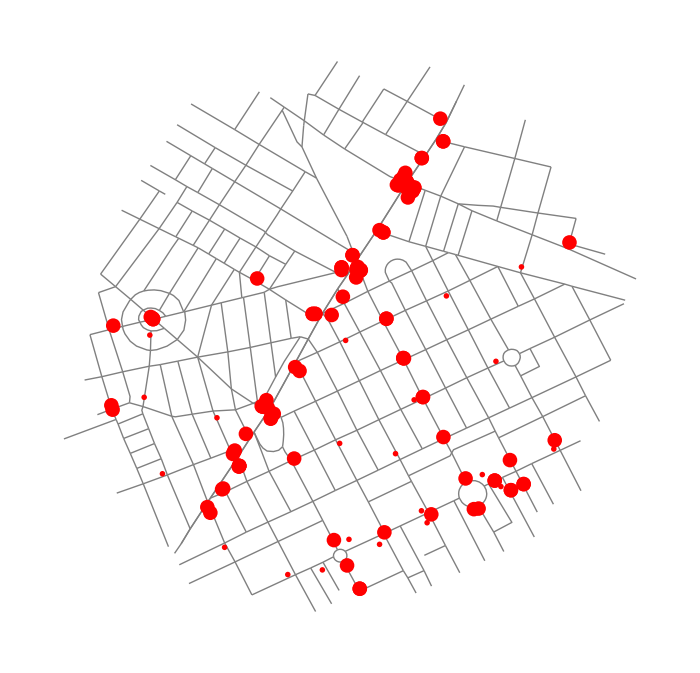

```mathematica
pl=Graphics[{Opacity[1],Gray,Thick,vias[[posv]],Black,EdgeForm[{Thin,Black,Dashed}],Opacity[0],circ,Opacity[1],Red,PointSize[0.015],puntos[[posc]],PointSize[0.025],Inset[logoe,ecobi[[1]],Scaled[{0.5,0.5}],0.0008],Map[Inset[logoe,#,Scaled[{0.5,0.5}],0.0006]&,ecobi[[npose]]]},ImageSize->700]
```

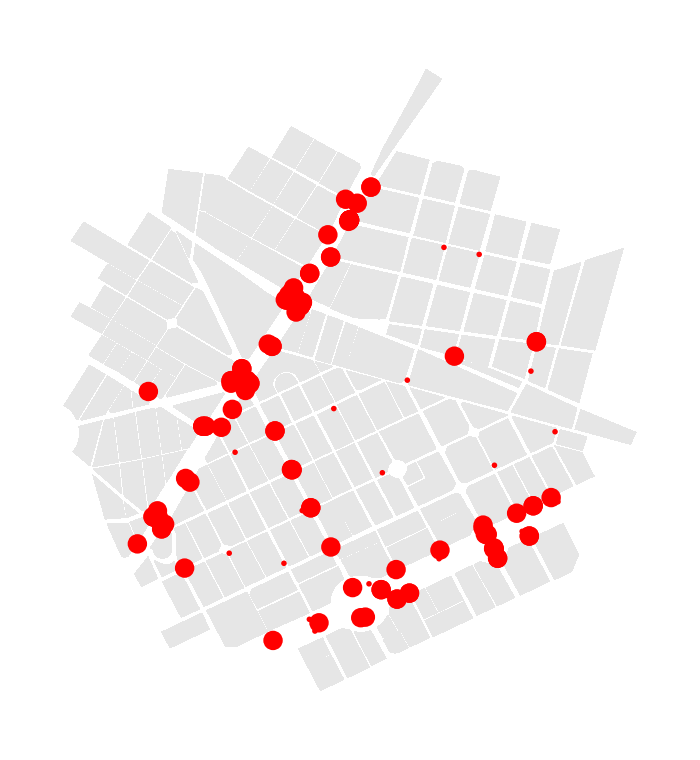

```mathematica
pl=Graphics[{Opacity[1],RGBColor[0.90,0.90,0.90],mans[[posa]],Black,EdgeForm[{Thin,Black,Dashed}],Opacity[0],circ,Opacity[1],Red,PointSize[0.02],puntos[[posc]],PointSize[0.035],Inset[logoe,ecobi[[1]],Scaled[{0.5,0.5}],0.0007],Map[Inset[logoe,#,Scaled[{0.5,0.5}],0.0004]&,ecobi[[nposm]]]},ImageSize->700]
```

```mathematica
Export["Pictures/MORLAN/ecobim.svg",pl,"SVG"]
Export["Pictures/MORLAN/ecobim.png",pl,"PNG"]
```

Pictures/MORLAN/ecobim.svg

Pictures/MORLAN/ecobim.png